# AndreasHafver/BayesianNetwork

Bayesian Networks for probabilistic analysis

## Paclet Manifest

"Documentation"

"English"

"Guides"

"ReferencePages"

"Symbols"

"BayesianNetwork.nb"DocumentationEnglishReferencePagesSymbolsBayesianNetwork.nb

"BayesianNetworkObject.nb"DocumentationEnglishReferencePagesSymbolsBayesianNetworkObject.nb

"Tutorials"

"Kernel"

"BayesianNetwork.wl"KernelBayesianNetwork.wl

"LICENSE"LICENSE

"PacletInfo.wl"PacletInfo.wl

"README.md"README.md

"ResourceDefinition.nb"ResourceDefinition.nb

"WLC post.nb"WLC post.nb

## Web Content

### Headline Image

### Basic Description

This is a simple implementation of Bayesian Networks (BNs) in the Wolfram Language. BNs are probabilistic graphical models for compactly representing multivariate probability distributions with conditional relationships among the variables. This implementation works with categorical (finite discrete) variables.

### Details

The Wolfram Language has extenive support for probabilistic computations, however there is no inbuilt support for graphical models.

This paclet provides a BayesianNetwork function that creates a BayesianNetworkObject. The BayesianNetworkObject can then be used with the function Probability to make inferences. The model can also be visualised using Graph.

This implementation allows the user to construct multivariate probability distribution bu defining each variable as an CategoricalDistribution or EmpiricalDistribution that may conditionally depend on each other.

An advantage of implementing BNs in Wolfram Language is that one can compute with symbolic probabilities. This means that one can do inference even when probabilities are unknown/difficult to specify and use the symbolic forms of the answer to gain insights about a system.

### Primary Context

andreashafver`BayesianNetwork`

### Main Guide Page

## Examples

### Initialization for Examples

```mathematica
PacletDirectoryLoad[NotebookDirectory[]];
```

```mathematica
Needs["andreashafver`BayesianNetwork`"];
```

### Basic Examples

Create a BN from a set of conditionally dependent univariate distributions:

```mathematica
cloudy = Function[CategoricalDistribution[{"True","False"},{0.5,0.5}]];
rain = Function[CategoricalDistribution[{"True","False"},Boole[#Cloudy=="True"]{0.8,0.2}+Boole[#Cloudy=="False"]{0.2,0.8}]];
sprinkler = Function[CategoricalDistribution[{"On","Off"},Boole[#Cloudy=="True"]{0.1,0.9}+Boole[#Cloudy=="False"]{0.5,0.5}]];
grass = Function[CategoricalDistribution[{"Wet","Dry"},Boole[#Rain=="True"&&#Sprinkler=="On"]{0.99,0.01}+ Boole[#Rain=="False"&&#Sprinkler=="On"]{0.9,0.1}+Boole[#Rain=="True"&&#Sprinkler=="Off"]{0.9,0.1}+Boole[#Rain=="False"&&#Sprinkler=="Off"]{0.0,1.0}]];

BN = BayesianNetwork[{
<|"Name"->"Cloudy","Distribution"->cloudy|>,
<|"Name"->"Rain","Distribution"->rain|>,
<|"Name"->"Sprinkler","Distribution"->sprinkler|>,
<|"Name"->"Grass","Distribution"->grass|>
}]
```

BayesianNetworkObject[…]

Do some computations:

```mathematica
Probability[#Cloudy =="True"\[Conditioned] #Rain =="True"&,BN]
```

0.8

Visualise the model:

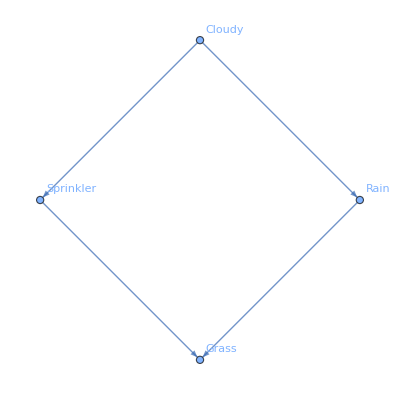

```mathematica
Graph[BN]
```

Visualise the model with some evidence:

```mathematica
Graph[BN, #Rain =="True"&]
```

-Graphics-

### Scope

Give more examples showing the range of features in the paclet:

Advanced inference is possible, beyond what is possible with other BN implementations:

```mathematica
BN = BayesianNetworkObject[…];
Probability[#Grass =="Wet"∧#Cloudy=="False"\[Conditioned] #Rain =="True"∨#Sprinkler == "On"&,BN]
Probability[#Grass =="Wet"⊽#Cloudy=="False"⊻#Sprinkler=="On"\[Conditioned] #Rain =="True"&,BN]
```

0.38662

0.073

A BN can be partially symbolic:

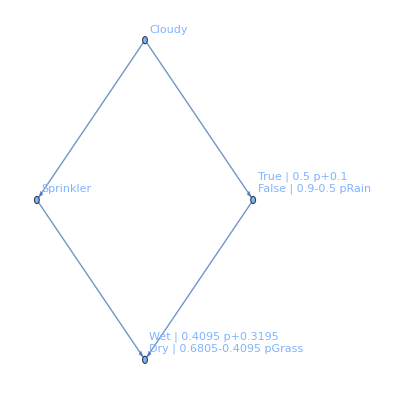

```mathematica
cloudy = Function[CategoricalDistribution[{"True","False"},{0.5,0.5}]];
rain = Function[CategoricalDistribution[{"True","False"},Boole[#Cloudy=="True"]{p,1-p}+Boole[#Cloudy=="False"]{0.2,0.8}]];
sprinkler = Function[CategoricalDistribution[{"On","Off"},Boole[#Cloudy=="True"]{0.1,0.9}+Boole[#Cloudy=="False"]{0.5,0.5}]];
grass = Function[CategoricalDistribution[{"Wet","Dry"},Boole[#Rain=="True"&&#Sprinkler=="On"]{0.99,0.01}+ Boole[#Rain=="False"&&#Sprinkler=="On"]{0.9,0.1}+Boole[#Rain=="True"&&#Sprinkler=="Off"]{0.9,0.1}+Boole[#Rain=="False"&&#Sprinkler=="Off"]{0.0,1.0}]];

BN = BayesianNetwork[{
<|"Name"->"Cloudy","Distribution"->cloudy|>,
<|"Name"->"Rain","Distribution"->rain|>,
<|"Name"->"Sprinkler","Distribution"->sprinkler|>,
<|"Name"->"Grass","Distribution"->grass|>
}];

Graph[BN]
```

A BN can be complete symbolic:

```mathematica
BN = BayesianNetwork[{
<|"Name"->"Cloudy","Distribution"->Function[CategoricalDistribution[{"True","False"},{pC,1-pC}]]|>,
<|"Name"->"Rain","Distribution"->Function[CategoricalDistribution[{"True","False"},Boole[#Cloudy=="True"]{pRc,1-pRc}+Boole[#Cloudy=="False"]{pRnc,1-pRnc}]]|>,
<|"Name"->"Sprinkler","Distribution"->Function[CategoricalDistribution[{"On","Off"},Boole[#Cloudy=="True"]{pSc,1-pSc}+Boole[#Cloudy=="False"]{pSnc,1-pSnc}]]|>,
<|"Name"->"Grass","Distribution"->Function[CategoricalDistribution[{"Wet","Dry"},Boole[#Rain=="True"&&#Sprinkler=="On"]{pGrs,1-pGrs}+ Boole[#Rain=="False"&&#Sprinkler=="On"]{pGnrs,1-pGnrs}+Boole[#Rain=="True"&&#Sprinkler=="Off"]{pGrns,1-pGrns}+Boole[#Rain=="False"&&#Sprinkler=="Off"]{pGnrns,1-pGnrns}]]|>
}];

Probability[#Cloudy== c\[Conditioned]#Grass=="Wet"&,BN]
```

(pC (pGnrns (-1+pRc) (-1+pSc)+(pGnrs-pGnrs pRc+pGrs pRc) pSc+pGrns (pRc-pRc pSc)) Boole[c==1]-(-1+pC) (pGnrns (-1+pRnc) (-1+pSnc)+(pGnrs-pGnrs pRnc+pGrs pRnc) pSnc+pGrns (pRnc-pRnc pSnc)) Boole[c==2])/(pGrns pRnc+pC pGrns (pRc-pRc pSc+pRnc (-1+pSnc))+pGnrns (-1+pRnc) (-1+pSnc)+pGnrs pSnc-pGnrs pRnc pSnc-pGrns pRnc pSnc+pGrs pRnc pSnc+pC pGnrs (pSc-pRc pSc+(-1+pRnc) pSnc)+pC pGrs (pRc pSc-pRnc pSnc)+pC pGnrns (pRnc+pRc (-1+pSc)-pSc+pSnc-pRnc pSnc))

## Source & Additional Information

### Creator

Andreas Hafver

### Source Control Repository

https://github.com/ahafver/BayesianNetwork

### License

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

Bayesian Network

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

### Original Source References and Attributions

### Links

### Compatibility

#### Wolfram Language Version

12.1+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

### Disclosures

Local filesDisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more information

Wolfram accountDisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more information

External servicesDisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more information

Wolfram Language system configurationDisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies $Path, Directory, or similar
◼ Installs additional paclets or dependencies
◼ Creates or imports non-public ResourceObject content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more information

Wolfram Language built-in symbolsDisclosuresWLSystemSymbolsChoose this option if your paclet directly modifies definitions of built-in symbols such as those in System` or other internal contexts.Click for more information

Paclet dependenciesDisclosuresPacletDependenciesChoose this option if your paclet directly installs or updates any additional paclets. Paclets that are included with the Wolfram system do not require a disclosure.Click for more information

OS configurationDisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of SystemCredentialClick for more information

Local system interactionsDisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via ExternalEvaluate
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more information

OtherDisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more information

## Author Notes

The author does not take responsibility for possible errors in this implementation!

Feel free to contact me if you have questions or suggestions to improve this paclet: ahafver@gmail.com